# A DLA choir

## Jovana Andrejevic, Nina Andrejevic, Amina Matt, and George Varnavides

```mathematica
URLShorten["https://www.wolframcloud.com/obj/amina.matt/Published/01_A_Choir_DLA.nb"]
```

https://wolfr.am/JEdwpG6p

```mathematica
NotebookOpen["https://wolfr.am/JEdwpG6p"]
```

vggft_shm27FrontEndObject[LinkObject["vggft_shm", 3, 1]]27JEdwpG6p/var/folders/3v/cd3_rvz10bd1jd08x0c03tpr0000gt/T/wolfr.am/JEdwpG6p

### We are combining audio with a DLA (Diffusion Limited Aggregation) algorithm.

### Sounds

#### Speak

```mathematica
Speak["Today we will program a DLA choir"]
```

#### A specific pitch with a duration and style

```mathematica
SoundNote[{"A1"},0.1,"VoiceAahs"]
```

SoundNote[{A1},0.1,VoiceAahs]

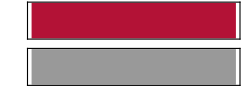

```mathematica
Sound[SoundNote[{"A1"},0.1,"VoiceAahs"]]
```

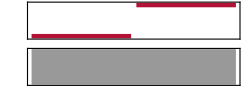

```mathematica
Sound[{SoundNote[{"C"},0.1,"VoiceAahs"],SoundNote[{"G"},0.1,"VoiceAahs"]}]
```

With the semitones given numerically and superposition

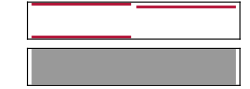

```mathematica
Sound[{SoundNote[{-5,7},0.1,"VoiceAahs"],SoundNote[6,0.1,"VoiceAahs"]}]
```

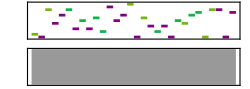

```mathematica
Sound[SoundNote[#,1,RandomChoice[{"Piano","Cello","Tuba"}]]& /@ RandomInteger[12, 30], 4]
```

#### An algorithmic composition with a Cellular Automaton

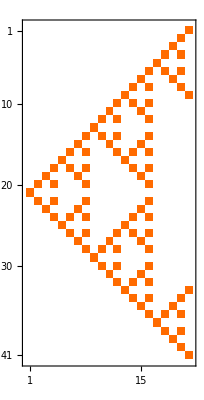

```mathematica
Transpose@CellularAutomaton[90,{{1},0},20]//MatrixPlot
```

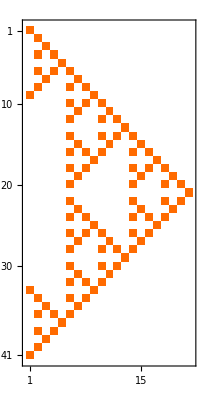

```mathematica
Reverse@#&/@Transpose[CellularAutomaton[90,{{1},0},20]]//MatrixPlot
```

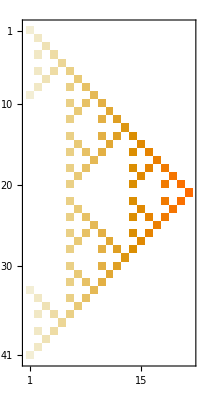

```mathematica
(3 Range[21]Reverse[#])&/@Transpose[CellularAutomaton[90,{{1},0},20]]//MatrixPlot
```

```mathematica
DeleteCases[(3 Range[21]Reverse[#]),0]&/@Transpose[CellularAutomaton[90,{{1},0},20]](*//MatrixPlot*)
```

{{3},{6},{9},{6,12},{15},{6,12,18},{9,21},{6,18,24},{3,27},{18,24,30},{21,33},{18,30,36},{39},{18,30,36,42},{21,33,45},{18,24,30,42,48},{27,51},{18,24,42,48,54},{21,45,57},{18,42,54,60},{63},{18,42,54,60},{21,45,57},{18,24,42,48,54},{27,51},{18,24,30,42,48},{21,33,45},{18,30,36,42},{39},{18,30,36},{21,33},{18,24,30},{3,27},{6,18,24},{9,21},{6,12,18},{15},{6,12},{9},{6},{3}}

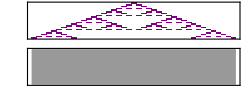

```mathematica
Sound[SoundNote[DeleteCases[3 Range[21]Reverse[#],0]-24(*3 octaves lower*),.1]&/@Transpose[CellularAutomaton[90,{{1},0},20]]]
```

#### From sinusoidal waves

```mathematica
Sound[{Play[Sin[1000t(1+t^2)],{t,0,.2}],Play[Sin[500t (1+t^3)],{t,0,.5}]}]
```

-Graphics-

Siren

```mathematica
f[t_,fc_,fm_,beta_]:=Sin[2*Pi*fc*t-beta*Sin[2*fm*Pi*t]]
```

```mathematica
f[t,1500,2,100]
```

Sin[3000 π t-100 Sin[4 π t]]

```mathematica
Sound[{Play[f[t,1500,2,100],{t,0,4}]}]
```

-Graphics-

```mathematica
Sound[{Play[f[t,1500,8,100],{t,0,4}]}]
```

-Graphics-

#### For our choir

```mathematica
lowNotes = {"A2","B2","C2", "D2", "E2","F2", "G2","A3","B3","C3", "D3", "E3","F3", "G3"};
```

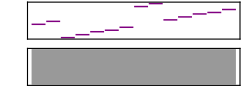

```mathematica
Sound[SoundNote[#]&/@lowNotes]
```

```mathematica
highNotes = {"A3","B3","C3", "D3", "E3","F3", "G3","A4","B4","C4", "D4", "E4","F4", "G4"};
```

```mathematica
Sound[SoundNote[#]&/@highNotes]
```

-Graphics-

```mathematica
notes:= Union[RandomSample[RandomChoice[{lowNotes,highNotes}], RandomInteger[{2,5}]]]
```

```mathematica
notes
```

{C3,D2,D3,G2,G3}

```mathematica
sounds := {
(*{notes,0.2,"VoiceOohs"}*)
{notes,0.5,"VoiceAahs"}
}
```

```mathematica
sounds
```

{{{B4,C3,D3,F3},0.5,VoiceAahs}}

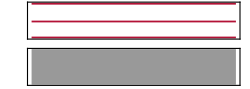

```mathematica
Sound[SoundNote@@RandomChoice[sounds]]
```

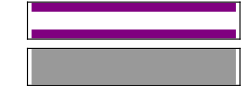

```mathematica
Sound[SoundNote[RandomChoice[sounds][[1]]]]
```

#### The DLA

#### A box with random walker starting along the edges

```mathematica
boxSize = 200;
alongEdge :=  RandomReal[{0,boxSize}];
numberWalkers = 75;
frozen = {{boxSize,boxSize}/2};
nf = Nearest[frozen];
```

```mathematica
(*A point somewhere on the fourth sides of the box*)
launchPoint := 
RandomChoice[
{{0,alongEdge},{alongEdge,0},{boxSize, alongEdge},{alongEdge,boxSize}}
]
```

```mathematica
walking = Table[launchPoint,{numberWalkers}];
```

```mathematica
walking
```

{{200,7.13317},{200,130.8},{189.082,200},{86.3122,200},{200,177.791},{200,181.167},{190.108,0},{32.5576,0},{0,108.689},{200,77.7592},{182.415,200},{181.274,0},{200,42.1258},{0,95.9387},{188.903,0},{47.5992,0},{0,69.2286},{27.2201,200},{0,28.2288},{0,9.62619},{200,0.632724},{0,145.952},{181.072,0},{55.3277,200},{0,108.25},{63.9967,200},{172.422,200},{200,167.681},{0,14.1147},{200,113.351},{155.523,200},{101.7,0},{48.9995,200},{172.069,200},{200,23.6185},{179.045,200},{200,147.414},{200,125.164},{200,144.167},{200,11.3549},{107.859,200},{200,82.6403},{130.481,0},{0,72.892},{130.92,0},{0,107.316},{15.3337,200},{148.063,0},{176.098,200},{76.4815,200},{0,41.0991},{139.498,0},{0,155.562},{40.8273,0},{200,88.4454},{186.944,0},{200,171.4},{0,187.649},{126.298,200},{0,169.06},{23.1825,200},{102.621,200},{109.786,0},{0,143.197},{0,118.06},{82.7828,0},{27.1388,200},{0,32.7349},{200,94.4979},{49.9475,200},{200,114.023},{41.5992,200},{47.3646,200},{115.953,0},{44.2866,0}}

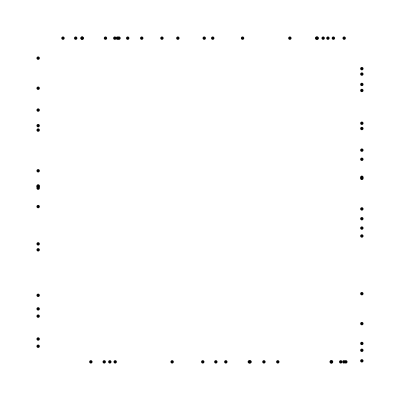

```mathematica
Graphics[{Disk[#]}&/@walking]
```

```mathematica
squareDistanceToClosestFrozen[position_, nf_]:= SquaredEuclideanDistance[position,nf[position][[1]]]
```

```mathematica
randomStep[position_, dxMax_]:= Mod[position+ RandomReal[{0,dxMax}]Through[{Cos,Sin}[RandomReal[{0,2Pi}]]],boxSize]
```

```mathematica
initialize:= Module[{},
boxSize = 200;
numberWalkers = 75;
frozen = {{boxSize,boxSize}/2};
walking = Table[launchPoint,{numberWalkers}];
nf = Nearest[frozen];
launchPoint := 
RandomChoice[
{{0,alongEdge},{alongEdge,0},{boxSize, alongEdge},{alongEdge,boxSize}}];
squareDistanceToClosestFrozen[position_, nf_]:= SquaredEuclideanDistance[position,nf[position][[1]]];
randomStep[position_, dxMax_]:= Mod[position+ RandomReal[{0,dxMax}]Through[{Cos,Sin}[RandomReal[{0,2Pi}]]],boxSize];
lowNotes = {"A2","B2","C2", "D2", "E2","F2", "G2","A3","B3","C3", "D3", "E3","F3", "G3"};
highNotes = {"A3","B3","C3", "D3", "E3","F3", "G3","A4","B4","C4", "D4", "E4","F4", "G4"};
notes:= Union[RandomSample[RandomChoice[{lowNotes,highNotes}], RandomInteger[{2,5}]]];
Sound[SoundNote[{"A"},0.1,"VoiceAahs"]];
sounds := {
(*{notes,0.2,"VoiceOohs"}*)
{notes,0.5,"VoiceAahs"}
};
]
```

```mathematica
dlaSimulaton:= 
Do[
walking = randomStep[#,2]&/@walking;
numberWalkers = Length[walking];
For[walker=1,walker≤ numberWalkers,walker++,
If[
squareDistanceToClosestFrozen[walking[[walker]],nf] ≤ 4,
(*Here is the sound*)
EmitSound@Sound[SoundNote@@RandomChoice[sounds]];
AppendTo[frozen,walking[[walker]]];
nf = Nearest[frozen];
walking[[walker]] = launchPoint;
];
]
,{100000}]
```

#### The EmitSound is necessary to Evaluate the wrapper.

#### With a nice interface

```mathematica
DefaultButton["Enjoy!",Speak["The push button is down at the bottom."];
CreateDocument[
{
Dynamic[
Graphics[
{
{FaceForm[RGBColor[0.65,0.74,1.]],EdgeForm[Black],Rectangle[{-1,-1},{boxSize+1,boxSize+1}]},
{GrayLevel[0.85],Disk[#,0.8]&/@walking},
{White,Disk[#,1.3]&/@frozen}
},
ImageSize-> Full
],Initialization:> initialize
],
DefaultButton["Push me!",dlaSimulaton,Method-> "Queued"]
}
],
Method->"Queued"
]
```

Enjoy!

```mathematica
frozen
```

{{100,100}}

#### With a signal when 5 of them have frozen and a techno touch

```mathematica
technoNotes = Table[i,{i,100,1000,100}];
```

```mathematica
f[t,#,2,100]&/@technoNotes
```

{Sin[200 π t-100 Sin[4 π t]],Sin[400 π t-100 Sin[4 π t]],Sin[600 π t-100 Sin[4 π t]],Sin[800 π t-100 Sin[4 π t]],Sin[1000 π t-100 Sin[4 π t]],Sin[1200 π t-100 Sin[4 π t]],Sin[1400 π t-100 Sin[4 π t]],Sin[1600 π t-100 Sin[4 π t]],Sin[1800 π t-100 Sin[4 π t]],Sin[2000 π t-100 Sin[4 π t]]}

```mathematica
(*EmitSound@*)Sound[{Play[f[t,#,2,100],{t,0,0.1}]}]&/@technoNotes
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
notes:= Union[RandomSample[RandomChoice[{technoNotes}], RandomInteger[{2,5}]]]
sounds := 
{Play[f[t,#,2,100],{t,0,0.2}]}&/@notes
```

```mathematica
sounds
```

{{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
initialize:= Module[{},
boxSize = 200;
numberWalkers = 150;
frozen = {{boxSize,boxSize}/2};
walking = Table[launchPoint,{numberWalkers}];
nf = Nearest[frozen];
launchPoint := 
RandomChoice[
{{0,alongEdge},{alongEdge,0},{boxSize, alongEdge},{alongEdge,boxSize}}];
squareDistanceToClosestFrozen[position_, nf_]:= SquaredEuclideanDistance[position,nf[position][[1]]];
randomStep[position_, dxMax_]:= Mod[position+ RandomReal[{0,dxMax}]Through[{Cos,Sin}[RandomReal[{0,2Pi}]]],boxSize];
(*Here*)
technoNotes = Table[i,{i,100,1000,100}];
notes:= Union[RandomSample[RandomChoice[{technoNotes}], RandomInteger[{2,5}]]];
sounds := 
{Play[f[t,#,2,100],{t,0,0.1}]}&/@notes;
;
]
```

#### Add the signal

```mathematica
siren=Sound[{Play[f[t,1500,2,100],{t,0,1}]}]
```

-Graphics-

```mathematica
initialize
```

```mathematica
If[
Mod[Dimensions[frozen][[1]],5]==0,EmitSound@siren,Nothing];
```

```mathematica
dlaSimulaton2:= 
Do[
walking = randomStep[#,2]&/@walking;
numberWalkers = Length[walking];
For[walker=1,walker≤ numberWalkers,walker++,
If[
squareDistanceToClosestFrozen[walking[[walker]],nf] ≤ 4,
(*Here is the signal*)
EmitSound@Sound[RandomChoice[sounds]];
If[Mod[Dimensions[frozen][[1]],5]==0,EmitSound@siren,Nothing];
AppendTo[frozen,walking[[walker]]];
nf = Nearest[frozen];
walking[[walker]] = launchPoint;
];
]
,{100000}]
```

```mathematica
DefaultButton["Enjoy!";
CreateDocument[
{
Dynamic[
Graphics[
{
{FaceForm[RGBColor[0.65,0.74,1.]],EdgeForm[Black],Rectangle[{-1,-1},{boxSize+1,boxSize+1}]},
{GrayLevel[0.85],Disk[#,0.8]&/@walking},
{White,Disk[#,1.3]&/@frozen}
},
ImageSize-> Full
],Initialization:> initialize
],
DefaultButton["Push me!",dlaSimulaton2,Method-> "Queued"]
}
],
Method->"Queued"
]
```

```mathematica
Sound[RandomChoice[sounds]]
```

-Graphics-

```mathematica
EmitSound@Sound[RandomChoice[sounds]]
```